## Import

```mathematica
$ProjectDir=FileNameJoin[{NotebookDirectory[],"..",".."}];
$ProjectMMADir="/home/ykm/文档/Wolfram Mathematica/[Work] Program_LargeIndexExpansion_2508";
```

```mathematica
Get[FileNameJoin[{$ProjectDir,"families","FamilyDatabase.wl"}]];
```

=== Registered IBP Families (27) ===

bub00 — 1-loop bubble, msq=0

bub10 — 1-loop bubble, msq=1

bub11 — 1-loop bubble, msq=1

Tri — 1-loop triangle, 3 props, s1=3,s2=8,s3=0

Box — 1-loop box, 4 props, s=3,t=2,u=-5

SR212 — Sunrise 2L1P, massless, s=1

SR212-3m — Sunrise 2L1P, 3-massive (props 1,3,5), s=3/2

SR212-5m — Sunrise 2L1P, all-massive, s=0

NP222 — Non-Planar 2L2P, s=1,s2=0,m=0

NP222var — NP 2L2P triangle, arXiv:2305.13951, k=0(fam b)

TB123 — Tri-Box 2L3P, massless, s=3,s1=2,s2=4

TB123m — Tri-Box 2L3P, massive, s=3,s1=2,s2=5,m=1

DB313 — Double Box 2L4P, s=2,t=3

DB313-4m — Double Box 2L4P, 4-massive (props 1,2,3,7), s=2,t=3,msq=1

NP322 — Non-Planar 2L4P, massless, s=1,t=5

NP322m — Non-Planar 2L4P, massive, s=3,t=2,m1=1,m2=4,m=1

DP323 — Double Pentagon 2L5P, s12=4,s13=7,s14=8,s23=1,s24=2,m=3

BN3L — 3-Loop Banana, vacuum, msq=1

BN3L1P — 3-Loop Banana 1-Point, massless, s=1

BN3L1Pm — 3-Loop Banana 1-Point, massive, s=1,msq=1

DP2L5P — Non-Planar DoublePentagon 2L5P massless, s12=3,s23=2,s34=5,s45=7,s15=11

HB2L5P — Non-Planar HexaBox 2L5P massless, s12=3,s23=2,s34=5,s45=7,s15=11

PB2L5P — Planar PentaBox 2L5P massless, s12=3,s23=2,s34=5,s45=7,s15=11

Penta1L — 1L Pentagon 5pt massless, s12=1,s23=2,s34=3,s45=5,s15=8

Penta1L-5m — 1L Pentagon 5pt all-massive, s12=1,s23=2,s34=3,s45=5,s15=8,msq=11

LA3L4Pm — 3L Ladder A 4pt 2-massive, s=3,t=2,m=1

LB3L4Pm — 3L Ladder B 4pt 2-massive, s=3,t=2,m=1

```mathematica
Get[FileNameJoin[{$ProjectMMADir,"SingularInterface.wl"}]];
Get[FileNameJoin[{$ProjectMMADir,"QuotientAlgebra.wl"}]];
Get[FileNameJoin[{$ProjectMMADir,"LargeIndexExpansion.wl"}]];
Get[FileNameJoin[{$ProjectMMADir,"BlockRecursion.wl"}]];Get[FileNameJoin[{$ProjectMMADir,"SymbolicBTForm.wl"}]];
```

```mathematica
Get[FileNameJoin[{$ProjectDir,"workspace","shared","VerifyUtility","ImportBinary_IBPMatrix.wl"}]];
```

```mathematica
Get[FileNameJoin[{$ProjectDir,"workspace","shared","VerifyUtility","ExportBinary_IBPMatrix.wl"}]];
```

```mathematica
Get[FileNameJoin[{$ProjectDir,"workspace","shared","VerifyUtility","AllRelationsToNuFormat.wl"}]];
```

```mathematica
polyVectorSort[polyVecList_,vlist_]:=Reverse@SortBy[polyVecList,Block[{i=1},While[#[[i]]==0,i++];If[i<=Length@polyVecList[[1]],Exponent[LT[#[[i]],vlist,"dp"],vlist]//{-i,Total[#],-Reverse@#}&,0]]&]
```

```mathematica
(* integrals are expressed by "j"[a1,a2,...]*)seriesVerify[AllRelations_,regionList_,seriesList_,vlist_,Alist_,modulus_]:=Module[{MatrixPowerMod,DotMod,rel0,rel,level,degree,varRule,limitSector,regionInfo,AMatrix,AMatInv,jsvar,relkey,relval,result,
verifyResult},
MatrixPowerMod[matrix_,matinv_,power_,mod_]:=Module[{},If[power>=0,
Nest[PolynomialMod[Dot[matrix,#],mod]&,IdentityMatrix@Length[matrix],power],
Nest[PolynomialMod[Dot[matinv,#],mod]&,IdentityMatrix@Length[matrix],-power]]];
DotMod[matList_,mod_]:=Module[{res=IdentityMatrix@Length[matList[[-1]]]},
Do[res=PolynomialMod[Dot[matList[[-i]],res],mod],{i,Length@matList}];res];

verifyResult=Table[{level,degree}=key;
If[AllRelations[key]=={},{},
rel0=AllRelations[key]/.{"j"[a__]:>js@@(vlist-{a})};

Table[regionInfo=regionList[[r]];
{varRule,limitSector}=regionInfo//{#["VarRule"],#["LimitSector"]}&;
rel=(rel0/n^degree)/.Thread[vlist->vlist+limitSector*n];
AMatrix=Table[
(Avar/.regionInfo["VarRule"])//monomialRulesPower[#,regionInfo["VarIndep"]]&//{Keys[#]/.regionInfo["MonomialBasisMatrix"],Values[#]}&//Sum[#[[1,i]]#[[2,i]],{i,Length@#[[1]]}]&,{Avar,Alist}];
AMatInv=Table[Inverse[Avar,Modulus->modulus],{Avar,AMatrix}];
relkey=Reverse@SortBy[#,{Total[List@@#],#}&]&@DeleteDuplicates@Cases[rel,_js,Infinity];
relval=Coefficient[#,relkey]&/@rel;relkey=List@@#&/@relkey;
relkey=Table[PolynomialMod[#,modulus]&@Dot[(DotMod[#,modulus]&@Table[MatrixPowerMod[AMatrix[[i]],AMatInv[[i]], -akey[[i]],modulus],{i,Length@AMatrix}]),(Sum[(1/n^k)seriesList[[r,k+1]]/.Thread[vlist -> vlist-akey],{k,0,order}])],{akey,relkey}];result=Table[Sum[PolynomialMod[Expand[relkey[[j]]relval[[k,j]]],modulus],{j,Length@relkey}]//CoefficientList[#,1/n,order+1]&//PolynomialMod[#,modulus]&,{k,Length@rel}];
Print["(lev,deg)=(",level,",",degree,")","    sector=",limitSector,"  (reg-",r,") : ",result//MatrixForm];
result
,{r,Length@regionList}]],
{key,Keys[AllRelations]}]
];
```

```mathematica
AMatrixRule[regionInfo_,Alist_,modulus_]:=Table[Avar->
((Avar/.regionInfo["VarRule"])//monomialRulesPower[#,regionInfo["VarIndep"]]&//{Keys[#]/.regionInfo["MonomialBasisMatrix"],Values[#]}&//Sum[#[[1,i]]#[[2,i]],{i,Length@#[[1]]}]&//PolynomialMod[#,modulus]&),{Avar,Alist}];
```

```mathematica
familyRootCount[expRegData_]:=(#->Total[Times@@(#["CoordinateRing"]["VarDeg"])&/@expRegData[#]])&/@Keys@expRegData;
```

## Test: bub00-1L2P

```mathematica
char=familydef["Modulus"];
```

```mathematica
famname="NP222";familydef=$FamilyDatabase[famname]
```

<|Description→Tri-Box 2L3P, massless, s=3,s1=2,s2=4,Propagators→{l1^2,(l1-p1)^2,(l1-p1-p2)^2,(l2+p1+p2)^2,l2^2,(l1+l2)^2,(l2+p1)^2},LoopMomenta→{l1,l2},ExternalMomenta→{p1,p2},KinematicRules→{p1^2→s1,p2^2→s2,p1 p2→1/2 (s-s1-s2)},TopSector→{1,1,1,1,1,1,0},Numeric→{s→3,s1→2,s2→4,msq→0,d→1/13},Modulus→179424673,Graph→{{1,4},{2,1},{5,2},{5,3},{3,4},{4,5}}|>

```mathematica
pdlist=familydef["Propagators"];loopmom=familydef["LoopMomenta"];extmom=familydef["ExternalMomenta"];spsRep=familydef["KinematicRules"];topsector=familydef["TopSector"];
numeric=familydef["Numeric"]/."d"->d;
{ne,nl,nE,nibp,Alist,vlist,ibpeqs1,sectorlist}=AsyIBPFamilyDefine[pdlist,loopmom,extmom,spsRep,topsector];
```

#IBP&LI: 9

```mathematica
AbsoluteTiming[expregdataFF=regionsBySectors[ibpeqs1/.numeric,sectorlist,Alist,vlist,Modulus->familydef["Modulus"]]][[1]]
```

#Non-triv Sectors = 31

10.0259

```mathematica
Print@MatrixForm[Join[{{"sector","#PD","#root","nb"}},
SortBy[(Join[{#,Total[#]},{Total[#],#}&[Times@@#["CoordinateRing"]["VarDeg"]&/@expregdataFF[#]]])&/@Keys@expregdataFF,{#[[2]],#[[1]]}&]]]
```

(sector | #PD | #root | nb
{0,0,0,0,1} | 1 | 1 | {1}
{0,0,0,1,0} | 1 | 1 | {1}
{0,0,1,0,0} | 1 | 1 | {1}
{0,1,0,0,0} | 1 | 1 | {1}
{1,0,0,0,0} | 1 | 1 | {1}
{0,0,0,1,1} | 2 | 1 | {1}
{0,0,1,0,1} | 2 | 1 | {1}
{0,0,1,1,0} | 2 | 1 | {1}
{0,1,0,0,1} | 2 | 1 | {1}
{0,1,0,1,0} | 2 | 1 | {1}
{0,1,1,0,0} | 2 | 1 | {1}
{1,0,0,0,1} | 2 | 1 | {1}
{1,0,0,1,0} | 2 | 1 | {1}
{1,0,1,0,0} | 2 | 1 | {1}
{1,1,0,0,0} | 2 | 1 | {1}
{0,0,1,1,1} | 3 | 3 | {1,1,1}
{0,1,0,1,1} | 3 | 5 | {1,1,1,2}
{0,1,1,0,1} | 3 | 5 | {2,3}
{0,1,1,1,0} | 3 | 3 | {1,2}
{1,0,0,1,1} | 3 | 3 | {1,1,1}
{1,0,1,0,1} | 3 | 5 | {1,4}
{1,0,1,1,0} | 3 | 5 | {1,1,3}
{1,1,0,0,1} | 3 | 3 | {1,2}
{1,1,0,1,0} | 3 | 5 | {2,3}
{1,1,1,0,0} | 3 | 3 | {1,2}
{0,1,1,1,1} | 4 | 5 | {1,1,1,2}
{1,0,1,1,1} | 4 | 5 | {1,1,3}
{1,1,0,1,1} | 4 | 5 | {2,3}
{1,1,1,0,1} | 4 | 5 | {5}
{1,1,1,1,0} | 4 | 5 | {2,3}
{1,1,1,1,1} | 5 | 21 | {1,2,2,16})

#### Check whether REGION INFO is in agreement

```mathematica
ibpmat1=ImportBinaryIBPMatrix[FileNameJoin[{$ProjectDir,"data","IBPMat_"<>famname<>".bin"}]];
ringdata1=ImportBinaryRingData[FileNameJoin[{$ProjectDir,"data","RingData_"<>famname<>".bin"}]];
```

Reading 49 regions from /home/ykm/Large-Index-Expansion-CPP/workspace/playground/../../data/IBPMat_Penta1L-5m.bin

Done: 49 regions loaded.

Reading 49 cells, ne=5 from /home/ykm/Large-Index-Expansion-CPP/workspace/playground/../../data/RingData_Penta1L-5m.bin

Done: 49 cells loaded.

```mathematica
ATableMMA=SortBy[({#["CoordinateRing"]["LimitSector"],(MatrixForm/@(Alist/.AMatrixRule[#["CoordinateRing"],Alist,char]))}&/@Join@@expregdataFF),{Total@#[[1]],#[[1]],#[[2]]}&];
ATableCPP=SortBy[({#["LimitSector"],MatrixForm/@#["FlatA"]})&/@ringdata1,{Total@#[[1]],#[[1]],#[[2]]}&];
```

```mathematica
secFilter[atab_,n_]:=Select[atab,Total@#[[1]]==n&];
```

```mathematica
proprank=3;
secCommon=Intersection[secFilter[ATableCPP,proprank][[;;,1]],secFilter[ATableMMA,proprank][[;;,1]]];
Print["Extra Sector:  \nCPP:  ",Complement[secFilter[ATableCPP,proprank][[;;,1]],secCommon],"\nMMA: ",Complement[secFilter[ATableMMA,proprank][[;;,1]],secCommon]]
```

Extra Sector:  
CPP:  {}
MMA: {{1,1,0,1,0}}

```mathematica
Complement[(Rule@@#&/@secFilter[ATableCPP,proprank]),(Rule@@#&/@secFilter[ATableMMA,proprank])]//MatrixForm
```

{}

```mathematica
Complement[(Rule@@#&/@secFilter[ATableMMA,proprank]),(Rule@@#&/@secFilter[ATableCPP,proprank])]//MatrixForm
```

({0,1,1,1,0}→{(118674917 | 140050016
95781680 | 66435946),(125603011 | 161484119
163435595 | 174094980),(1714083 | 30124448
159025309 | 78958904),(125603011 | 161484119
163435595 | 174094980),(0 | 105032531
1 | 71876111)}
{1,0,1,1,0}→{(10719827 | 176028082 | 953619
19342847 | 80949133 | 15428327
134450417 | 94747232 | 59056128),(123717193 | 117820106 | 75567525
98315435 | 165787499 | 72919205
86697349 | 55182333 | 171465411),(118131207 | 15722135 | 64042093
21326467 | 138947042 | 18910669
75265338 | 24816218 | 131312106),(46645738 | 71553594 | 45948283
55315010 | 145381904 | 49504186
58862619 | 18414477 | 33313579),(0 | 0 | 72190245
1 | 0 | 52022764
0 | 1 | 30303777)}
{1,1,0,1,0}→{(88391563 | 156898107
131037241 | 121241437),(104726908 | 118533639
28350017 | 23787208),(164925418 | 55231085
138468355 | 98039078),(119807050 | 136763855
116915474 | 136510377),(0 | 49133874
1 | 52069044)}
{1,1,0,1,0}→{(18195856 | 107241101 | 82477053
109700240 | 57967560 | 17552757
93702434 | 77041955 | 98147290),(55379824 | 13159401 | 165526799
158674315 | 54467989 | 4341
1370746 | 12411541 | 148449703),(162766723 | 61805375 | 12636766
78476971 | 159236075 | 87590870
125010395 | 133268026 | 105470586),(132229722 | 5520615 | 10355698
144496621 | 10939125 | 123638546
19315573 | 64817975 | 61353720),(0 | 0 | 17584137
1 | 0 | 73134665
0 | 1 | 157584629)}
{1,1,1,0,0}→{(15123341 | 38524320
25911006 | 78737488),(143681678 | 79812092
141966608 | 152867088),(15123341 | 38524320
25911006 | 78737488),(128091176 | 81796597
178253254 | 175534661),(0 | 26739195
1 | 131092876)})

```mathematica
Print["MMA:  A=\n",(Rule@@#&/@secFilter[ATableMMA,proprank])//MatrixForm];
Print["C++:  A=\n",(Rule@@#&/@secFilter[ATableCPP,proprank])//MatrixForm];
(*Print["diff:  A=\n",Select[secFilter[ATableCPP,proprank],MemberQ[secCommon,#[[1]]]&][[;;,2]]-Select[secFilter[ATableMMA,proprank],MemberQ[secCommon,#[[1]]]&][[;;,2]]//MatrixForm];*)
```

MMA:  A=
({0,0,1,1,1}→{(35467466),(9722818),(104314585),(37526997),(104314585)}
{0,0,1,1,1}→{(52895118),(45561487),(38563597),(165412827),(38563597)}
{0,0,1,1,1}→{(150337096),(59593302),(167832837),(90664186),(167832837)}
{0,1,0,1,1}→{(5876871),(173367968),(14857299),(95372302),(41813647)}
{0,1,0,1,1}→{(26525757),(133542055),(160655745),(26105753),(141338206)}
{0,1,0,1,1}→{(168996707),(102985453),(137372070),(82756316),(73943414)}
{0,1,0,1,1}→{(92890955 | 158543534
62848367 | 52882097),(113512917 | 41766262
127722423 | 95386655),(98888478 | 15038609
156784994 | 8876970),(161588624 | 135109853
62972501 | 162353531),(0 | 29698675
1 | 143438599)}
{0,1,1,0,1}→{(112960962 | 91000152
96216013 | 37679503),(95104494 | 91321350
15407068 | 134472253),(73849128 | 147895753
100073662 | 107882660),(50472911 | 20591712
138812372 | 90120135),(0 | 26681561
1 | 109610246)}
{0,1,1,0,1}→{(1665769 | 107107049 | 37702846
171024416 | 81893091 | 137521039
6131546 | 115956634 | 3155656),(48985025 | 115897802 | 128394108
129182782 | 90719725 | 63224457
78705654 | 85615644 | 72574415),(62705271 | 144808279 | 9653311
111403449 | 5482088 | 9289418
52372773 | 43336769 | 171708942),(83387401 | 50090180 | 53056737
25307506 | 98110661 | 142675911
26821083 | 17483530 | 138090435),(0 | 0 | 28598103
1 | 0 | 86017104
0 | 1 | 85109065)}
{0,1,1,1,0}→{(174684483),(76239419),(33506350),(76239419),(83992021)}
{0,1,1,1,0}→{(118674917 | 140050016
95781680 | 66435946),(125603011 | 161484119
163435595 | 174094980),(1714083 | 30124448
159025309 | 78958904),(125603011 | 161484119
163435595 | 174094980),(0 | 105032531
1 | 71876111)}
{1,0,0,1,1}→{(20631185),(146843749),(105476155),(20631185),(80700659)}
{1,0,0,1,1}→{(118545316),(4128303),(123323572),(118545316),(151736885)}
{1,0,0,1,1}→{(141462090),(123897953),(75378039),(141462090),(61166466)}
{1,0,1,0,1}→{(157795955),(116725478),(95633847),(151294627),(116871470)}
{1,0,1,0,1}→{(168482951 | 44571811 | 147646071 | 160632542
7048103 | 103505456 | 14855353 | 164522185
31824693 | 78433261 | 69611149 | 78648069
128546491 | 76575004 | 126816877 | 28636507),(120719655 | 52986544 | 63629083 | 93547256
86013177 | 22326457 | 10874227 | 29801129
16721347 | 37345969 | 157616413 | 19053692
17774319 | 24441954 | 94666533 | 37246196),(56375691 | 12103100 | 90473809 | 51308557
139555851 | 80190464 | 10904474 | 88726754
88083059 | 167286912 | 29229226 | 178405178
98116784 | 69385829 | 43788736 | 120596460),(169780530 | 43966031 | 160979614 | 16546379
157107276 | 86949304 | 59933308 | 151460646
137024513 | 47865974 | 34416225 | 87261582
79974509 | 26873538 | 151375000 | 156219541),(0 | 0 | 0 | 53368901
1 | 0 | 0 | 43127606
0 | 1 | 0 | 31918997
0 | 0 | 1 | 47037544)}
{1,0,1,1,0}→{(46341069),(137938918),(173212493),(178659294),(170710163)}
{1,0,1,1,0}→{(154887103),(69078935),(162165177),(72374083),(91859109)}
{1,0,1,1,0}→{(10719827 | 176028082 | 953619
19342847 | 80949133 | 15428327
134450417 | 94747232 | 59056128),(123717193 | 117820106 | 75567525
98315435 | 165787499 | 72919205
86697349 | 55182333 | 171465411),(118131207 | 15722135 | 64042093
21326467 | 138947042 | 18910669
75265338 | 24816218 | 131312106),(46645738 | 71553594 | 45948283
55315010 | 145381904 | 49504186
58862619 | 18414477 | 33313579),(0 | 0 | 72190245
1 | 0 | 52022764
0 | 1 | 30303777)}
{1,1,0,0,1}→{(152697494),(179354611),(160073414),(61319280),(179354611)}
{1,1,0,0,1}→{(64521838 | 42545940
111261581 | 76384678),(0 | 22047617
1 | 79814361),(97429736 | 4174067
135374044 | 51147301),(101849299 | 37035688
138019816 | 17855320),(0 | 22047617
1 | 79814361)}
{1,1,0,1,0}→{(88391563 | 156898107
131037241 | 121241437),(104726908 | 118533639
28350017 | 23787208),(164925418 | 55231085
138468355 | 98039078),(119807050 | 136763855
116915474 | 136510377),(0 | 49133874
1 | 52069044)}
{1,1,0,1,0}→{(18195856 | 107241101 | 82477053
109700240 | 57967560 | 17552757
93702434 | 77041955 | 98147290),(55379824 | 13159401 | 165526799
158674315 | 54467989 | 4341
1370746 | 12411541 | 148449703),(162766723 | 61805375 | 12636766
78476971 | 159236075 | 87590870
125010395 | 133268026 | 105470586),(132229722 | 5520615 | 10355698
144496621 | 10939125 | 123638546
19315573 | 64817975 | 61353720),(0 | 0 | 17584137
1 | 0 | 73134665
0 | 1 | 157584629)}
{1,1,1,0,0}→{(173189847),(176479917),(173189847),(17086168),(35858772)}
{1,1,1,0,0}→{(15123341 | 38524320
25911006 | 78737488),(143681678 | 79812092
141966608 | 152867088),(15123341 | 38524320
25911006 | 78737488),(128091176 | 81796597
178253254 | 175534661),(0 | 26739195
1 | 131092876)})

C++:  A=
({0,0,1,1,1}→{(35467466),(9722818),(104314585),(37526997),(104314585)}
{0,0,1,1,1}→{(52895118),(45561487),(38563597),(165412827),(38563597)}
{0,0,1,1,1}→{(150337096),(59593302),(167832837),(90664186),(167832837)}
{0,1,0,1,1}→{(5876871),(173367968),(14857299),(95372302),(41813647)}
{0,1,0,1,1}→{(26525757),(133542055),(160655745),(26105753),(141338206)}
{0,1,0,1,1}→{(168996707),(102985453),(137372070),(82756316),(73943414)}
{0,1,0,1,1}→{(92890955 | 158543534
62848367 | 52882097),(113512917 | 41766262
127722423 | 95386655),(98888478 | 15038609
156784994 | 8876970),(161588624 | 135109853
62972501 | 162353531),(0 | 29698675
1 | 143438599)}
{0,1,1,0,1}→{(112960962 | 91000152
96216013 | 37679503),(95104494 | 91321350
15407068 | 134472253),(73849128 | 147895753
100073662 | 107882660),(50472911 | 20591712
138812372 | 90120135),(0 | 26681561
1 | 109610246)}
{0,1,1,0,1}→{(1665769 | 107107049 | 37702846
171024416 | 81893091 | 137521039
6131546 | 115956634 | 3155656),(48985025 | 115897802 | 128394108
129182782 | 90719725 | 63224457
78705654 | 85615644 | 72574415),(62705271 | 144808279 | 9653311
111403449 | 5482088 | 9289418
52372773 | 43336769 | 171708942),(83387401 | 50090180 | 53056737
25307506 | 98110661 | 142675911
26821083 | 17483530 | 138090435),(0 | 0 | 28598103
1 | 0 | 86017104
0 | 1 | 85109065)}
{0,1,1,1,0}→{(174684483),(76239419),(33506350),(76239419),(83992021)}
{1,0,0,1,1}→{(20631185),(146843749),(105476155),(20631185),(80700659)}
{1,0,0,1,1}→{(118545316),(4128303),(123323572),(118545316),(151736885)}
{1,0,0,1,1}→{(141462090),(123897953),(75378039),(141462090),(61166466)}
{1,0,1,0,1}→{(157795955),(116725478),(95633847),(151294627),(116871470)}
{1,0,1,0,1}→{(168482951 | 44571811 | 147646071 | 160632542
7048103 | 103505456 | 14855353 | 164522185
31824693 | 78433261 | 69611149 | 78648069
128546491 | 76575004 | 126816877 | 28636507),(120719655 | 52986544 | 63629083 | 93547256
86013177 | 22326457 | 10874227 | 29801129
16721347 | 37345969 | 157616413 | 19053692
17774319 | 24441954 | 94666533 | 37246196),(56375691 | 12103100 | 90473809 | 51308557
139555851 | 80190464 | 10904474 | 88726754
88083059 | 167286912 | 29229226 | 178405178
98116784 | 69385829 | 43788736 | 120596460),(169780530 | 43966031 | 160979614 | 16546379
157107276 | 86949304 | 59933308 | 151460646
137024513 | 47865974 | 34416225 | 87261582
79974509 | 26873538 | 151375000 | 156219541),(0 | 0 | 0 | 53368901
1 | 0 | 0 | 43127606
0 | 1 | 0 | 31918997
0 | 0 | 1 | 47037544)}
{1,0,1,1,0}→{(46341069),(137938918),(173212493),(178659294),(170710163)}
{1,0,1,1,0}→{(154887103),(69078935),(162165177),(72374083),(91859109)}
{1,1,0,0,1}→{(152697494),(179354611),(160073414),(61319280),(179354611)}
{1,1,0,0,1}→{(64521838 | 42545940
111261581 | 76384678),(0 | 22047617
1 | 79814361),(97429736 | 4174067
135374044 | 51147301),(101849299 | 37035688
138019816 | 17855320),(0 | 22047617
1 | 79814361)}
{1,1,1,0,0}→{(173189847),(176479917),(173189847),(17086168),(35858772)})

Thread::tdlen: … 中长度不相等的对象无法合并.

diff:  A=
{{(35467466),(9722818),(104314585),(37526997),(104314585)},{(52895118),(45561487),(38563597),(165412827),(38563597)},{(150337096),(59593302),(167832837),(90664186),(167832837)},{(5876871),(173367968),(14857299),(95372302),(41813647)},{(26525757),(133542055),(160655745),(26105753),(141338206)},{(168996707),(102985453),(137372070),(82756316),(73943414)},{(92890955 | 158543534
62848367 | 52882097),(113512917 | 41766262
127722423 | 95386655),(98888478 | 15038609
156784994 | 8876970),(161588624 | 135109853
62972501 | 162353531),(0 | 29698675
1 | 143438599)},{(112960962 | 91000152
96216013 | 37679503),(95104494 | 91321350
15407068 | 134472253),(73849128 | 147895753
100073662 | 107882660),(50472911 | 20591712
138812372 | 90120135),(0 | 26681561
1 | 109610246)},{(1665769 | 107107049 | 37702846
171024416 | 81893091 | 137521039
6131546 | 115956634 | 3155656),(48985025 | 115897802 | 128394108
129182782 | 90719725 | 63224457
78705654 | 85615644 | 72574415),(62705271 | 144808279 | 9653311
111403449 | 5482088 | 9289418
52372773 | 43336769 | 171708942),(83387401 | 50090180 | 53056737
25307506 | 98110661 | 142675911
26821083 | 17483530 | 138090435),(0 | 0 | 28598103
1 | 0 | 86017104
0 | 1 | 85109065)},{(174684483),(76239419),(33506350),(76239419),(83992021)},{(20631185),(146843749),(105476155),(20631185),(80700659)},{(118545316),(4128303),(123323572),(118545316),(151736885)},{(141462090),(123897953),(75378039),(141462090),(61166466)},{(157795955),(116725478),(95633847),(151294627),(116871470)},{(168482951 | 44571811 | 147646071 | 160632542
7048103 | 103505456 | 14855353 | 164522185
31824693 | 78433261 | 69611149 | 78648069
128546491 | 76575004 | 126816877 | 28636507),(120719655 | 52986544 | 63629083 | 93547256
86013177 | 22326457 | 10874227 | 29801129
16721347 | 37345969 | 157616413 | 19053692
17774319 | 24441954 | 94666533 | 37246196),(56375691 | 12103100 | 90473809 | 51308557
139555851 | 80190464 | 10904474 | 88726754
88083059 | 167286912 | 29229226 | 178405178
98116784 | 69385829 | 43788736 | 120596460),(169780530 | 43966031 | 160979614 | 16546379
157107276 | 86949304 | 59933308 | 151460646
137024513 | 47865974 | 34416225 | 87261582
79974509 | 26873538 | 151375000 | 156219541),(0 | 0 | 0 | 53368901
1 | 0 | 0 | 43127606
0 | 1 | 0 | 31918997
0 | 0 | 1 | 47037544)},{(46341069),(137938918),(173212493),(178659294),(170710163)},{(154887103),(69078935),(162165177),(72374083),(91859109)},{(152697494),(179354611),(160073414),(61319280),(179354611)},{(64521838 | 42545940
111261581 | 76384678),(0 | 22047617
1 | 79814361),(97429736 | 4174067
135374044 | 51147301),(101849299 | 37035688
138019816 | 17855320),(0 | 22047617
1 | 79814361)},{(173189847),(176479917),(173189847),(17086168),(35858772)}}+{{-(35467466),-(9722818),-(104314585),-(37526997),-(104314585)},{-(52895118),-(45561487),-(38563597),-(165412827),-(38563597)},{-(150337096),-(59593302),-(167832837),-(90664186),-(167832837)},{-(5876871),-(173367968),-(14857299),-(95372302),-(41813647)},{-(26525757),-(133542055),-(160655745),-(26105753),-(141338206)},{-(168996707),-(102985453),-(137372070),-(82756316),-(73943414)},{-(92890955 | 158543534
62848367 | 52882097),-(113512917 | 41766262
127722423 | 95386655),-(98888478 | 15038609
156784994 | 8876970),-(161588624 | 135109853
62972501 | 162353531),-(0 | 29698675
1 | 143438599)},{-(112960962 | 91000152
96216013 | 37679503),-(95104494 | 91321350
15407068 | 134472253),-(73849128 | 147895753
100073662 | 107882660),-(50472911 | 20591712
138812372 | 90120135),-(0 | 26681561
1 | 109610246)},{-(1665769 | 107107049 | 37702846
171024416 | 81893091 | 137521039
6131546 | 115956634 | 3155656),-(48985025 | 115897802 | 128394108
129182782 | 90719725 | 63224457
78705654 | 85615644 | 72574415),-(62705271 | 144808279 | 9653311
111403449 | 5482088 | 9289418
52372773 | 43336769 | 171708942),-(83387401 | 50090180 | 53056737
25307506 | 98110661 | 142675911
26821083 | 17483530 | 138090435),-(0 | 0 | 28598103
1 | 0 | 86017104
0 | 1 | 85109065)},{-(174684483),-(76239419),-(33506350),-(76239419),-(83992021)},{-(118674917 | 140050016
95781680 | 66435946),-(125603011 | 161484119
163435595 | 174094980),-(1714083 | 30124448
159025309 | 78958904),-(125603011 | 161484119
163435595 | 174094980),-(0 | 105032531
1 | 71876111)},{-(20631185),-(146843749),-(105476155),-(20631185),-(80700659)},{-(118545316),-(4128303),-(123323572),-(118545316),-(151736885)},{-(141462090),-(123897953),-(75378039),-(141462090),-(61166466)},{-(157795955),-(116725478),-(95633847),-(151294627),-(116871470)},{-(168482951 | 44571811 | 147646071 | 160632542
7048103 | 103505456 | 14855353 | 164522185
31824693 | 78433261 | 69611149 | 78648069
128546491 | 76575004 | 126816877 | 28636507),-(120719655 | 52986544 | 63629083 | 93547256
86013177 | 22326457 | 10874227 | 29801129
16721347 | 37345969 | 157616413 | 19053692
17774319 | 24441954 | 94666533 | 37246196),-(56375691 | 12103100 | 90473809 | 51308557
139555851 | 80190464 | 10904474 | 88726754
88083059 | 167286912 | 29229226 | 178405178
98116784 | 69385829 | 43788736 | 120596460),-(169780530 | 43966031 | 160979614 | 16546379
157107276 | 86949304 | 59933308 | 151460646
137024513 | 47865974 | 34416225 | 87261582
79974509 | 26873538 | 151375000 | 156219541),-(0 | 0 | 0 | 53368901
1 | 0 | 0 | 43127606
0 | 1 | 0 | 31918997
0 | 0 | 1 | 47037544)},{-(46341069),-(137938918),-(173212493),-(178659294),-(170710163)},{-(154887103),-(69078935),-(162165177),-(72374083),-(91859109)},{-(10719827 | 176028082 | 953619
19342847 | 80949133 | 15428327
134450417 | 94747232 | 59056128),-(123717193 | 117820106 | 75567525
98315435 | 165787499 | 72919205
86697349 | 55182333 | 171465411),-(118131207 | 15722135 | 64042093
21326467 | 138947042 | 18910669
75265338 | 24816218 | 131312106),-(46645738 | 71553594 | 45948283
55315010 | 145381904 | 49504186
58862619 | 18414477 | 33313579),-(0 | 0 | 72190245
1 | 0 | 52022764
0 | 1 | 30303777)},{-(152697494),-(179354611),-(160073414),-(61319280),-(179354611)},{-(64521838 | 42545940
111261581 | 76384678),-(0 | 22047617
1 | 79814361),-(97429736 | 4174067
135374044 | 51147301),-(101849299 | 37035688
138019816 | 17855320),-(0 | 22047617
1 | 79814361)},{-(173189847),-(176479917),-(173189847),-(17086168),-(35858772)},{-(15123341 | 38524320
25911006 | 78737488),-(143681678 | 79812092
141966608 | 152867088),-(15123341 | 38524320
25911006 | 78737488),-(128091176 | 81796597
178253254 | 175534661),-(0 | 26739195
1 | 131092876)}}

```mathematica
Print["diff:  A=\n",Sort@ATableCPP[[;;,2]]-Sort@ATableMMA[[;;,2]]];
```

```mathematica
ibpmatKeys=(ibpmat1[[1]]//Keys)[[6;;-1]]
```

{M1,N1,K1,F0,F2,K1s,K2s,F2s}

```mathematica
Print["MMA:  ibpmat=\n",MatrixForm/@(Normal@expregdataFF[[1,1]]["RecursionMatrix"][#]&/@ibpmatKeys)];
Print["C++:  ibpmat=\n",MatrixForm/@(Normal[ibpmat1[[1]][#]]&/@ibpmatKeys)];
Print["diff:  ibpmat=\n",(Normal[ibpmat1[[1]][#]&/@ibpmatKeys]-(Normal@expregdataFF[[1,1]]["RecursionMatrix"][#]&/@ibpmatKeys))//PolynomialMod[#,char]&//Flatten]
```

MMA:  ibpmat=
{((1) | (0) | (3) | (0) | (0)
(0) | (179424671) | (179424671) | (0) | (0)
(2) | (2) | (0) | (0) | (0)
(8) | (0) | (179424663) | (18) | (0)
(179424657) | (0) | (16) | (179424655) | (10)),((179424671) | (0) | (2) | (99680375) | (71769868)
(2) | (179424671) | (179424671) | (79744298) | (71769876)
(2) | (2) | (179424671) | (79744298) | (143539734)
(8) | (0) | (179424665) | (99680373) | (179424669)
(179424657) | (179424645) | (16) | (39872150) | (71769870)),((0) | (1) | (3) | (99680376) | (71769869)
(1) | (179424672) | (179424671) | (79744298) | (71769876)
(2) | (1) | (179424672) | (79744298) | (143539734)
(8) | (0) | (179424664) | (99680374) | (179424669)
(179424657) | (179424645) | (16) | (39872149) | (71769871)),((119616449)
(0)
(0)
(0)
(0)),(((0)
(1)
(179424672)
(79744299)
(71769869)) | ((0)
(0)
(0)
(0)
(0)) | ((0)
(0)
(0)
(0)
(0)) | ((0)
(0)
(0)
(0)
(0)) | ((0)
(0)
(0)
(0)
(0))
((0)
(179424672)
(1)
(99680374)
(107654804)) | ((1)
(0)
(1)
(99680374)
(107654804)) | ((0)
(0)
(0)
(0)
(0)) | ((0)
(0)
(0)
(0)
(0)) | ((0)
(0)
(0)
(0)
(0))
((0)
(0)
(0)
(0)
(0)) | ((179424672)
(0)
(179424672)
(79744299)
(71769869)) | ((179424672)
(1)
(0)
(79744299)
(71769869)) | ((0)
(0)
(0)
(0)
(0)) | ((0)
(0)
(0)
(0)
(0))
((0)
(0)
(0)
(0)
(0)) | ((0)
(0)
(0)
(0)
(0)) | ((1)
(179424672)
(0)
(99680374)
(107654804)) | ((179424664)
(9)
(179424664)
(0)
(107654802)) | ((0)
(0)
(0)
(0)
(0))
((0)
(0)
(0)
(0)
(0)) | ((0)
(0)
(0)
(0)
(0)) | ((0)
(0)
(0)
(0)
(0)) | ((9)
(179424664)
(9)
(0)
(71769871)) | ((179424668)
(5)
(179424668)
(39872149)
(0))),((0) | (0) | (3) | (0) | (0)
(1) | (0) | (179424671) | (0) | (0)
(2) | (0) | (179424672) | (0) | (0)
(8) | (0) | (179424664) | (0) | (0)
(179424657) | (0) | (16) | (0) | (0)),((179424672) | (0) | (0) | (0) | (0)
(1) | (2) | (0) | (0) | (0)
(0) | (179424671) | (179424672) | (0) | (0)
(0) | (0) | (1) | (179424655) | (0)
(0) | (0) | (0) | (18) | (179424663)),(((0)
(0)
(179424672)
(0)
(0)) | ((0)
(0)
(0)
(0)
(0)) | ((0)
(0)
(0)
(0)
(0)) | ((0)
(0)
(0)
(0)
(0)) | ((0)
(0)
(0)
(0)
(0))
((0)
(0)
(1)
(0)
(0)) | ((1)
(0)
(1)
(0)
(0)) | ((0)
(0)
(0)
(0)
(0)) | ((0)
(0)
(0)
(0)
(0)) | ((0)
(0)
(0)
(0)
(0))
((0)
(0)
(0)
(0)
(0)) | ((179424672)
(0)
(179424672)
(0)
(0)) | ((179424672)
(0)
(0)
(0)
(0)) | ((0)
(0)
(0)
(0)
(0)) | ((0)
(0)
(0)
(0)
(0))
((0)
(0)
(0)
(0)
(0)) | ((0)
(0)
(0)
(0)
(0)) | ((1)
(0)
(0)
(0)
(0)) | ((179424664)
(0)
(179424664)
(0)
(0)) | ((0)
(0)
(0)
(0)
(0))
((0)
(0)
(0)
(0)
(0)) | ((0)
(0)
(0)
(0)
(0)) | ((0)
(0)
(0)
(0)
(0)) | ((9)
(0)
(9)
(0)
(0)) | ((179424668)
(0)
(179424668)
(0)
(0)))}

C++:  ibpmat=
{((1) | (0) | (3) | (0) | (0)
(0) | (179424671) | (179424671) | (0) | (0)
(2) | (2) | (0) | (0) | (0)
(8) | (0) | (179424663) | (18) | (0)
(179424657) | (0) | (16) | (179424655) | (10)),((179424671) | (0) | (2) | (99680375) | (71769868)
(2) | (179424671) | (179424671) | (79744298) | (71769876)
(2) | (2) | (179424671) | (79744298) | (143539734)
(8) | (0) | (179424665) | (99680373) | (179424669)
(179424657) | (179424645) | (16) | (39872150) | (71769870)),((0) | (1) | (3) | (99680376) | (71769869)
(1) | (179424672) | (179424671) | (79744298) | (71769876)
(2) | (1) | (179424672) | (79744298) | (143539734)
(8) | (0) | (179424664) | (99680374) | (179424669)
(179424657) | (179424645) | (16) | (39872149) | (71769871)),((119616449)
(0)
(0)
(0)
(0)),(((0)
(1)
(179424672)
(79744299)
(71769869)) | ((0)
(0)
(0)
(0)
(0)) | ((0)
(0)
(0)
(0)
(0)) | ((0)
(0)
(0)
(0)
(0)) | ((0)
(0)
(0)
(0)
(0))
((0)
(179424672)
(1)
(99680374)
(107654804)) | ((1)
(0)
(1)
(99680374)
(107654804)) | ((0)
(0)
(0)
(0)
(0)) | ((0)
(0)
(0)
(0)
(0)) | ((0)
(0)
(0)
(0)
(0))
((0)
(0)
(0)
(0)
(0)) | ((179424672)
(0)
(179424672)
(79744299)
(71769869)) | ((179424672)
(1)
(0)
(79744299)
(71769869)) | ((0)
(0)
(0)
(0)
(0)) | ((0)
(0)
(0)
(0)
(0))
((0)
(0)
(0)
(0)
(0)) | ((0)
(0)
(0)
(0)
(0)) | ((1)
(179424672)
(0)
(99680374)
(107654804)) | ((179424664)
(9)
(179424664)
(0)
(107654802)) | ((0)
(0)
(0)
(0)
(0))
((0)
(0)
(0)
(0)
(0)) | ((0)
(0)
(0)
(0)
(0)) | ((0)
(0)
(0)
(0)
(0)) | ((9)
(179424664)
(9)
(0)
(71769871)) | ((179424668)
(5)
(179424668)
(39872149)
(0))),((0) | (0) | (3) | (0) | (0)
(1) | (0) | (179424671) | (0) | (0)
(2) | (0) | (179424672) | (0) | (0)
(8) | (0) | (179424664) | (0) | (0)
(179424657) | (0) | (16) | (0) | (0)),((179424672) | (0) | (0) | (0) | (0)
(1) | (2) | (0) | (0) | (0)
(0) | (179424671) | (179424672) | (0) | (0)
(0) | (0) | (1) | (179424655) | (0)
(0) | (0) | (0) | (18) | (179424663)),(((0)
(0)
(179424672)
(0)
(0)) | ((0)
(0)
(0)
(0)
(0)) | ((0)
(0)
(0)
(0)
(0)) | ((0)
(0)
(0)
(0)
(0)) | ((0)
(0)
(0)
(0)
(0))
((0)
(0)
(1)
(0)
(0)) | ((1)
(0)
(1)
(0)
(0)) | ((0)
(0)
(0)
(0)
(0)) | ((0)
(0)
(0)
(0)
(0)) | ((0)
(0)
(0)
(0)
(0))
((0)
(0)
(0)
(0)
(0)) | ((179424672)
(0)
(179424672)
(0)
(0)) | ((179424672)
(0)
(0)
(0)
(0)) | ((0)
(0)
(0)
(0)
(0)) | ((0)
(0)
(0)
(0)
(0))
((0)
(0)
(0)
(0)
(0)) | ((0)
(0)
(0)
(0)
(0)) | ((1)
(0)
(0)
(0)
(0)) | ((179424664)
(0)
(179424664)
(0)
(0)) | ((0)
(0)
(0)
(0)
(0))
((0)
(0)
(0)
(0)
(0)) | ((0)
(0)
(0)
(0)
(0)) | ((0)
(0)
(0)
(0)
(0)) | ((9)
(0)
(9)
(0)
(0)) | ((179424668)
(0)
(179424668)
(0)
(0)))}

diff:  ibpmat=
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
expregdataFF[[1,1]]["RecursionMatrix"]//Keys
```

{M1,N1,K1,K1s,K2s,F2,F2s,F0,nibp,ne,nb,incre}

```mathematica
Normal[ibpmat1[[1]][#]&/@ibpmatKeys]-(Normal@expregdataFF[[1,1]]["RecursionMatrix"][#]&/@ibpmatKeys)
```

{{{{{0}},{{0}}},{{{0}},{{0}}}},{{{{0}},{{0}}},{{{0}},{{0}}}},{{{{0}},{{0}}},{{{0}},{{0}}}},{{{0}},{{0}}},{{{{{0}},{{0}}},{{{0}},{{0}}}},{{{{0}},{{0}}},{{{0}},{{0}}}}},{{{{0}},{{0}}},{{{0}},{{0}}}},{{{{0}},{{0}}},{{{0}},{{0}}}},{{{{{0}},{{0}}},{{{0}},{{0}}}},{{{{0}},{{0}}},{{{0}},{{0}}}}}}

{{{{{1}},{{3}}},{{{179424671}},{{2}}}},{{{{179424671}},{{2}}},{{{179424669}},{{4}}}},{{{{0}},{{3}}},{{{179424670}},{{3}}}},{{{119616449}},{{0}}},{{{{{0}},{{179424672}}},{{{0}},{{0}}}},{{{{0}},{{179424672}}},{{{1}},{{0}}}}},{{{{0}},{{3}}},{{{179424670}},{{3}}}},{{{{179424672}},{{0}}},{{{179424672}},{{1}}}},{{{{{0}},{{179424672}}},{{{0}},{{0}}}},{{{{0}},{{179424672}}},{{{1}},{{0}}}}}}

## Test: Compare Penta1L-5m

```mathematica
famname="Penta1L-5m";
expregdataFF=Get[FileNameJoin[{NotebookDirectory[],famname<>"-expreg.m"}]];
```

```mathematica
ibpmat1=ImportBinaryIBPMatrix[FileNameJoin[{$ProjectDir,"workspace/C022-Penta1L-5m-region-solve-cpp/output/IBPMat_Penta1L-5m.bin"}]];
ringdata1=ImportBinaryRingData[FileNameJoin[{$ProjectDir,"workspace/C022-Penta1L-5m-region-solve-cpp/output/RingData_Penta1L-5m.bin"}]];
```

Reading 56 regions from /home/ykm/Large-Index-Expansion-CPP/workspace/playground/../../workspace/C022-Penta1L-5m-region-solve-cpp/output/IBPMat_Penta1L-5m.bin

Done: 56 regions loaded.

Reading 56 cells, ne=5 from /home/ykm/Large-Index-Expansion-CPP/workspace/playground/../../workspace/C022-Penta1L-5m-region-solve-cpp/output/RingData_Penta1L-5m.bin

Done: 56 cells loaded.

```mathematica
ringdata1[[1]]
```

<|LimitSector→{0,0,0,0,1},nb→1,FlatA→{{{16311334}},{{119616449}},{{156996589}},{{16311334}},{{16311334}}},FlatAinv→{{{11}},{{3}},{{8}},{{11}},{{11}}}|>

```mathematica
ringdata1[[1]]["FlatA"]
```

{{{16311334}},{{119616449}},{{156996589}},{{16311334}},{{16311334}}}

```mathematica
ringdata1[[-1]]["LimitSector"]
```

{1,1,1,1,1}

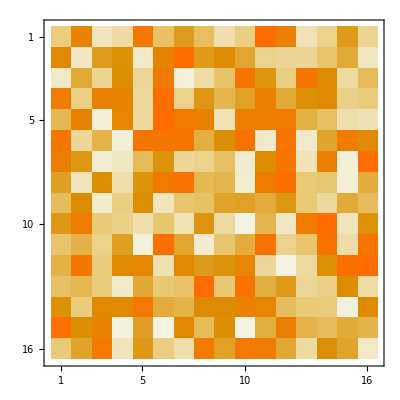
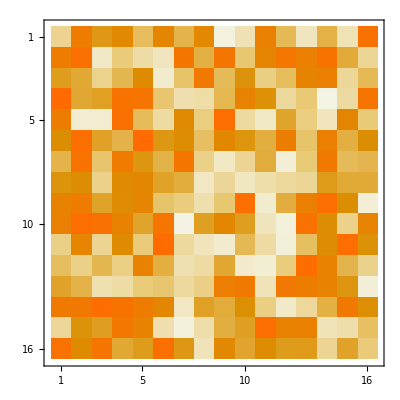
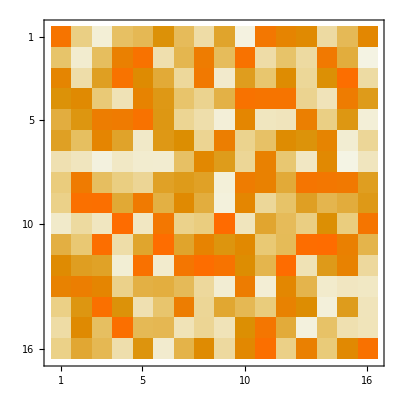
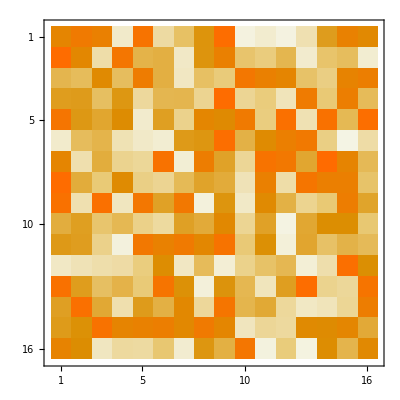
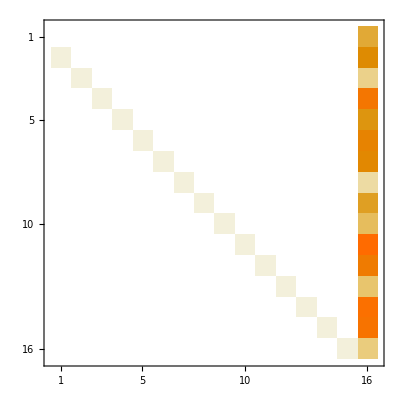

```mathematica
MatrixPlot/@ringdata1[[-1]]["FlatA"]
```

```mathematica
(List/@Range[0,15])/.expregdataFF[{1,1,1,1,1}][[4]]["CoordinateRing"]["MonomialBasisMatrix"]
```

```mathematica
char=familydef["Modulus"]
```

179424673

```mathematica
Map[MatrixPlot,M1MMA,1]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
M1CPP=ringdata1[[-1]]["FlatA"];M1MMA=(Alist/.expregdataFF[{1,1,1,1,1}][[4]]["CoordinateRing"]["VarRule"]//Map[PolynomialMod[#,char]&@Sum[#[[i]]({i-1}/.expregdataFF[{1,1,1,1,1}][[4]]["CoordinateRing"]["MonomialBasisMatrix"]),{i,16}]&@CoefficientList[#,A[5],16]&,#,1]&);
M1CPP-M1MMA
```

{{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}}

```mathematica
Map[MatrixPlot,M1CPP,1]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Map[MatrixPlot,M1MMA,1]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Alist/.expregdataFF[{0,0,0,0,1}][[1]]["CoordinateRing"]["VarRule"]
```

{16311334,119616449,156996589,16311334,16311334}

```mathematica
ibpmat1[[1]]["M1"]//MatrixForm
```

((179424672) | (0) | (0) | (0) | (179424672)
(1) | (130490671) | (0) | (0) | (0)
(0) | (48934002) | (48934001) | (0) | (0)
(0) | (0) | (130490672) | (179424672) | (0)
(0) | (0) | (0) | (1) | (179424672))

```mathematica
Normal@expregdataFF[{0,0,0,0,1}][[1]]["RecursionMatrix"]["M1"]//Map[PolynomialMod[-#,char]&,#,{3}]&//MatrixForm
```

((179424672) | (0) | (0) | (0) | (179424672)
(1) | (130490671) | (0) | (0) | (0)
(0) | (48934002) | (48934001) | (0) | (0)
(0) | (0) | (130490672) | (179424672) | (0)
(0) | (0) | (0) | (1) | (179424672))

((-1) | (0) | (0) | (0) | (-1)
(-179424672) | (-48934002) | (0) | (0) | (0)
(0) | (-130490671) | (-130490672) | (0) | (0)
(0) | (0) | (-48934001) | (-1) | (0)
(0) | (0) | (0) | (-179424672) | (-1))

```mathematica
expregdataFF[{0,0,0,0,1}][[1]]["CoordinateRing"]["VarRule"]
```

{A[5]→16311334,A[4]→16311334,A[3]→156996589,A[2]→119616449,A[1]→16311334}

```mathematica
expregdataFF[{0,0,0,0,1}][[1]]["RecursionMatrix"]["M1"]
```

SparseArray[…]

```mathematica
Print@MatrixForm[Join[{{"sector","#PD","#root","nb"}},
(SortBy[Join@@#&/@Transpose[{{#,Total[#]}&/@Keys[#],{Total[#],#}&/@Map[#[[2]]&,Values[#],{2}]}]&@GroupBy[#,#[[1]]&]&[{#["LimitSector"],#["nb"]}&/@ringdata1],{#[[2]],#[[1]]}&])]]
```

(sector | #PD | #root | nb
{0,0,0,0,1} | 1 | 1 | {1}
{0,0,0,1,0} | 1 | 1 | {1}
{0,0,1,0,0} | 1 | 1 | {1}
{0,1,0,0,0} | 1 | 1 | {1}
{1,0,0,0,0} | 1 | 1 | {1}
{0,0,0,1,1} | 2 | 1 | {1}
{0,0,1,0,1} | 2 | 1 | {1}
{0,0,1,1,0} | 2 | 1 | {1}
{0,1,0,0,1} | 2 | 1 | {1}
{0,1,0,1,0} | 2 | 1 | {1}
{0,1,1,0,0} | 2 | 1 | {1}
{1,0,0,0,1} | 2 | 1 | {1}
{1,0,0,1,0} | 2 | 1 | {1}
{1,0,1,0,0} | 2 | 1 | {1}
{1,1,0,0,0} | 2 | 1 | {1}
{0,0,1,1,1} | 3 | 3 | {1,1,1}
{0,1,0,1,1} | 3 | 5 | {1,1,1,2}
{0,1,1,0,1} | 3 | 5 | {2,3}
{0,1,1,1,0} | 3 | 3 | {1,2}
{1,0,0,1,1} | 3 | 3 | {1,1,1}
{1,0,1,0,1} | 3 | 5 | {1,4}
{1,0,1,1,0} | 3 | 5 | {1,1,3}
{1,1,0,0,1} | 3 | 3 | {1,2}
{1,1,0,1,0} | 3 | 5 | {2,3}
{1,1,1,0,0} | 3 | 3 | {1,2}
{0,1,1,1,1} | 4 | 5 | {1,1,1,2}
{1,0,1,1,1} | 4 | 5 | {1,1,3}
{1,1,0,1,1} | 4 | 5 | {2,3}
{1,1,1,0,1} | 4 | 5 | {5}
{1,1,1,1,0} | 4 | 5 | {2,3}
{1,1,1,1,1} | 5 | 21 | {1,2,2,16})(sector | #PD | #root | nb
{0,0,0,0,1} | 1 | 1 | {1}
{0,0,0,1,0} | 1 | 1 | {1}
{0,0,1,0,0} | 1 | 1 | {1}
{0,1,0,0,0} | 1 | 1 | {1}
{1,0,0,0,0} | 1 | 1 | {1}
{0,0,0,1,1} | 2 | 1 | {1}
{0,0,1,0,1} | 2 | 1 | {1}
{0,0,1,1,0} | 2 | 1 | {1}
{0,1,0,0,1} | 2 | 1 | {1}
{0,1,0,1,0} | 2 | 1 | {1}
{0,1,1,0,0} | 2 | 1 | {1}
{1,0,0,0,1} | 2 | 1 | {1}
{1,0,0,1,0} | 2 | 1 | {1}
{1,0,1,0,0} | 2 | 1 | {1}
{1,1,0,0,0} | 2 | 1 | {1}
{0,0,1,1,1} | 3 | 3 | {1,1,1}
{0,1,0,1,1} | 3 | 5 | {1,1,1,2}
{0,1,1,0,1} | 3 | 5 | {2,3}
{0,1,1,1,0} | 3 | 3 | {1,2}
{1,0,0,1,1} | 3 | 3 | {1,1,1}
{1,0,1,0,1} | 3 | 5 | {1,4}
{1,0,1,1,0} | 3 | 5 | {1,1,3}
{1,1,0,0,1} | 3 | 3 | {1,2}
{1,1,0,1,0} | 3 | 5 | {2,3}
{1,1,1,0,0} | 3 | 3 | {1,2}
{0,1,1,1,1} | 4 | 5 | {1,1,1,2}
{1,0,1,1,1} | 4 | 5 | {1,1,3}
{1,1,0,1,1} | 4 | 5 | {2,3}
{1,1,1,0,1} | 4 | 5 | {5}
{1,1,1,1,0} | 4 | 5 | {2,3}
{1,1,1,1,1} | 5 | 21 | {1,2,2,16})